```mathematica
CloseKernels[];
LaunchKernels[8];
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<GeneralRelativityTensors`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"]
ParallelNeeds["KerrGeodesics`"]
ParallelNeeds["GeneralRelativityTensors`"]
ParallelNeeds["Teukolsky`"]
prec=40;
```

```mathematica
αstring=Import["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TPPM\\TPPMStringTable..a0..p20..e0..ra4..rb100..regionI..LMAX20..NMAX0.dat"];
αs =Uncompress[αstring[[1,1]]];
α[s_,l_,m_,n_]:=Uncompress[αs[[If[s==-1,1,2], l,m +l+1,1]]];
```

```mathematica
𝔰[sp_,l_,lp_, m_]:= -sp  Sqrt[(2(2l+1))/(2 lp +1)]ClebschGordan[{l,m},{1,0},{lp,m}] ClebschGordan[{l,-sp} ,{1,sp }, {lp ,0}]
Ccoef[s_,j_,k_,m_,bs_]:=𝔰[s,j,k,m]*(j/.bs);
CLcoef [a_,m_,n_,j_,k_,ω_, bs_]:=(j/.bs)*(Sqrt[j(j+1)] KroneckerDelta[j,k] - a ω 𝔰[+1, j,k,m]);
```

```mathematica
Rs = Uncompress[Import["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TRadialStringTable..a0..p20..e0..LMAX20..NMAX10.dat"][[1,1]]];
R[s_,l_,m_,n_]:= Uncompress[Rs[[If[s==-1,1,2], l,m +l+1, n+11]]]
```

```mathematica
Fr0[a_,τ_,  orbit_, k_,m_,n_, LMAX_]:= Module[{A,B,t, r,θ,φ, tdot, phidot,  rmin, rmax},
{t,r,θ,φ}=orbit["Trajectory"];

Sum[Module[{bsplus,bsminus,χ, g, dP, K0,Β,Pminus, Pplus,Rminus,  Δ, λ, Σ, cl, cp, cm},
bsplus = SpinWeightedSpheroidalHarmonicS[1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX}]["ExpansionCoefficients"] ;
bsminus = SpinWeightedSpheroidalHarmonicS[-1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX}]["ExpansionCoefficients"] ;
cl =CLcoef[a, m, n ,j,k,ω[m,n],bsplus];
cp = Ccoef[1, j, k, m , bsplus];
cm = Ccoef[-1, j,k,m, bsminus];
If[cl ==0&&cp==0&&cl==0,0,
λ = SpinWeightedSpheroidalEigenvalue[-1,l,m,a ω[m,n]];
Β= Sqrt[λ^2+ 4 a m ω[m,n] - 4 a^2 ω[m,n]^2];
K0= ω[m,n]((r[τ])^2 + a^2)- a m;

Pminus= R[-1,l,m,n]["In"][r[τ]];
Δ=r[τ]^2-2 M r[τ] + a^2/.M->1;
Σ=r[τ]^2+ a^2 Cos[θ[τ]]^2;
Pplus = Δ R[1,l,m,n]["In"][r[τ]];
dP =R[-1,l,m,n]["In"]'[r[τ]];

g= 1/Β (r[τ] dP- ⅈ K0 r[τ]/Δ Pminus-Pminus);
χ=Exp[-ⅈ ω[m,n] t[τ] + ⅈ m φ[τ]];

A = Re[χ(cl g + ⅈ a cp/Β (dP - ⅈ K0/Δ ))];
B= Im[
χ(cm*α[-1,l,m,n][r[τ]]Pminus - cp* α[1,l,m,n][r[τ]] Pplus)];
tmp=(Sqrt[2] (t'[τ] - a φ'[τ]))/(r[τ]^2 Σ)A + (φ'[τ] *(a^2+r[τ]^2) + a t'[τ])/(Sqrt[2] Δ r[τ] Σ)B;
tmp
]
],{l,Max[1,Abs[m]],LMAX}, {j, k-1, k+1}]
]
```

```mathematica
tmp
```

tmp

```mathematica
Off[ClebschGordan::tri ]
Off[ClebschGordan::phy]
```

```mathematica
ParallelEvaluate[Off[ClebschGordan::tri ]]
ParallelEvaluate[Off[ClebschGordan::phy]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
AbsoluteTiming[With[{a=SetPrecision[0,prec], e=SetPrecision[0,prec],p=SetPrecision[20,prec],x=1, τ=0.5,LMAX= 20,NMax=0},
q=1;
orbit = KerrGeoOrbit[a,p,e,x]; 
Ω =KerrGeoFrequencies[a,p,e,x];
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
kmodes = Monitor[ParallelTable[
Sum[Fr0[a,τ,  orbit,k ,m,n, LMAX], {m,-k,k}, {n,-NMax, NMax}],{k,1,20}]
,{k,m,n}]
]]
```

{299.132,{3.23431,111.886,3972.13,135528.,4.84831×10^6,1.66959×10^8,6.02448×10^9,2.08271×10^11,7.53401×10^12,2.6038×10^14,9.39871×10^15,3.23789×10^17,1.16224×10^19,3.98282×10^20,1.4177×10^22,4.82974×10^23,1.6987×10^25,5.89764×10^26,1.99133×10^28,6.78923×10^29}}

```mathematica
data = Table[{i, Log[Abs[kmodes[[i]]]]},{i,1,20}];
fit = Fit[data, {1,y},y]
```

-2.38198+3.55689 y

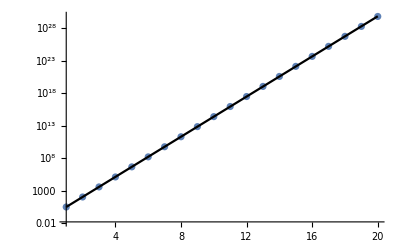

```mathematica
Show[ListLogPlot[{Abs[kmodes]}, PlotRange->{{1,20},All}], Plot[fit/.y->xx,{xx,1,20}, PlotStyle->{Black}]]
```

```mathematica
w
```

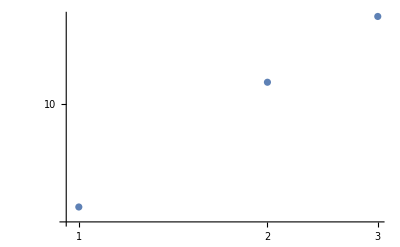

```mathematica
ListLogLogPlot[Table[{k,Log[kmodes[[k]]]}, {k,1,3}]]
```

```mathematica
(*Configurable*)
prec = 40;
a= 0;
p=10;
e=0.1;
ra = 4;
rb = 100;
dr = 1;
region = "ℋ";
LMAX=20;
NMAX=10;
dir = "/users/smp22ejg/conservativeSelfForce/TPPM/";

(*Set Precisions*)
aa = SetPrecision[a,prec];
pp = SetPrecision[p,prec];
ee = SetPrecision[e,prec];
x = 1;

(*Calculate Orbits*)
orbit = KerrGeoOrbit[aa, pp, ee, x];

mode = TeukolskyPointParticleMode[-1,7,2,0,orbit];
rs =Table[{r,mode["ExtendedHomogeneous"->region][r]},{r,ra,rb,dr}]
```

{{4,1.4205094944712851911083305416×10^-6-0.000030615608529776018274438025657 ⅈ},{5,0.000017860365705898500211243471329-0.000341198552322041521309258361412 ⅈ},{6,0.00012626576603618754363611773742-0.00213264001033325313737581880748 ⅈ},{7,0.00062414860571274019546317752865-0.00939166391839696949463403217682 ⅈ},{8,0.0024134029778666062062714735997-0.0326500411407782936218044629903 ⅈ},{9,0.0077979385291840260300357255394-0.0956748139437524226499543949336 ⅈ},{10,0.021964175339343313797629371256-0.246292898559110791699389588104 ⅈ},{11,0.055507551969994826380124567326-0.572724736717502539483155340074 ⅈ},{12,0.12847356854823494844589233841-1.226952994434243019680038258 ⅈ},{13,0.27649693576147451931944935844-2.45678055206872735868319536928 ⅈ},{14,0.55974543349700024469135204595-4.64833513435987151236871557149 ⅈ},{15,1.0755042717998872305162687645-8.38085405417938344640062875241 ⅈ},{16,1.9753701470502575581939284054-14.4956300880292217177532216595 ⅈ},{17,3.4881597527740158353611279201-24.1810171160370899392991918396 ⅈ},{18,5.9497731098599911656761362386-39.0753807608680184916147142786 ⅈ},{19,9.841385533853146911136633532-61.3898340414409956188998128651 ⅈ},{20,15.83747112149977069568895786-94.0525204969817932535906927738 ⅈ},{21,24.86528305407532551748608348-140.876097105718438340663384632 ⅈ},{22,38.17752951582690889401902936-206.749926689033861314481064862 ⅈ},{23,57.4400863625215331264361329-297.85831472530987415498728551 ⅈ},{24,84.836676634408655358416405956-421.92591926860169392047475319 ⅈ},{25,123.19252043362035380113366208-588.49122594631823960402186289 ⅈ},{26,176.11901449920839932502187078-809.20871406450242010749107524 ⅈ},{27,248.18153703211213612664442173-1098.1800462373701467627201282 ⅈ},{28,345.09248808283381880070551941-1472.3142945210463291810598441 ⅈ},{29,473.93166738797017161558095452-1951.7168728850320068123016125 ⅈ},{30,643.39605835383071684904627643-2560.1064813756844650352293946 ⅈ},{31,864.08102753372288725838525193-3325.2589841387018745420387415 ⅈ},{32,1148.7948622158177606628847473-4279.4767444294131755393718075 ⅈ},{33,1512.9084536200023379410207404-5460.0815279225970918962786212 ⅈ},{34,1974.741788901463741033749918-6909.928664305326254076229214 ⅈ},{35,2555.988741112847761900852298-8677.939729739653697419233683 ⅈ},{36,3282.181442164070154893876011-10819.650582912259287617293837 ⅈ},{37,4183.195289568784704894296328-13397.77115877002354243828432 ⅈ},{38,5293.795373567907721842793781-16482.75300050280250860738809 ⅈ},{39,6654.224817527818437297443059-20153.360095784806661309898851 ⅈ},{40,8310.835202048388436495634069-24497.238181682972180728889722 ⅈ},{41,10316.75889298118737841238163-29611.477297967700574753065533 ⅈ},{42,12732.62271682210635212790934-35603.162004797445336847806426 ⅈ},{43,15627.30202524888195000913494-42589.903341840352012887857469 ⅈ},{44,19078.71376573582100386273192-50700.346295728598784258810003 ⅈ},{45,23174.64672927324170468723129-60074.646265109014362587915977 ⅈ},{46,28013.62668158324365915994148-70864.907771132649693529507839 ⅈ},{47,33705.81360344065777825759822-83235.578459544341341719236553 ⅈ},{48,40373.92777160064860099774781-97363.79128194340399085468707 ⅈ},{49,48154.20090744999227497265646-113439.647631437911018222849 ⅈ},{50,57197.34810909587328027615125-131666.4341447275046579689298 ⅈ},{51,67669.55576763698698884930967-152260.7658712881637732910776 ⅈ},{52,79753.48015345619386300248081-175452.6485531822132927935376 ⅈ},{53,93649.25084731827622936221131-201485.4528581609286055348548 ⅈ},{54,109575.472687772657853576189-230615.7935659241428510787187 ⅈ},{55,127770.2194148847117292494789-263113.3069240661049890436417 ⅈ},{56,148492.0117147754157227124294-299260.319667422180333648853 ⅈ},{57,172020.7719140269831380273829-339351.4035329112906320764921 ⅈ},{58,198658.7471419394575399754393-383692.8095018263290257995555 ⅈ},{59,228731.3923761393200340508443-432601.7764627368872337514819 ⅈ},{60,262588.2044173688450171847329-486405.7095101992091190156635 ⅈ},{61,300603.4975066026101891175646-545441.2236763597182313008612 ⅈ},{62,343177.1110060502470283322633-610053.0495329069474037766466 ⅈ},{63,390735.0393191148956004895425-680592.7977978598812359677462 ⅈ},{64,443729.9740268561318573126254-757417.5808331379533802926435 ⅈ},{65,502641.7480736650941299605675-840888.489722073093044664271 ⅈ},{66,567977.6717462195823400818746-931368.9264679111644217910343 ⅈ},{67,640272.7501606518131559636358-1.029222791751410884566946416×10^6 ⅈ},{68,720089.772006289641857275998-1.134812529623983725119030654×10^6 ⅈ},{69,808019.259393109364144529677-1.248497031488141562638060176×10^6 ⅈ},{70,904679.268816652229403992279-1.370629402724671365647055308×10^6 ⅈ},{71,1.01071503349077176707134895×10^6-1.50155459636092620261749949×10^6 ⅈ},{72,1.1267984376070122923195576×10^6-1.64160691923156532836299434×10^6 ⅈ},{73,1.2536273134611188455169298×10^6-1.79110741715634025725825855×10^6 ⅈ},{74,1.39192455284320414884733596×10^6-1.95036114674317268081072321×10^6 ⅈ},{75,1.54243702461909951894323136×10^6-2.11965434251261278632397619×10^6 ⅈ},{76,1.70593429103661961243769485×10^6-2.29925148912538677273103869×10^6 ⅈ},{77,1.88320711597166119516758341×10^6-2.48939230957153071060548501×10^6 ⅈ},{78,2.0750657590845672886078725×10^6-2.69028868124079546230591358×10^6 ⅈ},{79,2.28233805068589097581918829×10^6-2.90212149283270120197703762×10^6 ⅈ},{80,2.50586724301098836167060596×10^6-3.12503745607383998168837305×10^6 ⅈ},{81,2.74650963457268248206105088×10^6-3.35914588718274157181336418×10^6 ⅈ},{82,3.00513196529801568483780885×10^6-3.60451547395179247304413956×10^6 ⅈ},{83,3.28260858125581497608497757×10^6-3.86117104519432196685501558×10^6 ⅈ},{84,3.57981836894292495878370665×10^6-4.12909036012610501596620844×10^6 ⅈ},{85,3.89764146031453771725660913×10^6-4.40820093600735505459782146×10^6 ⅈ},{86,4.23695571101362745200221366×10^6-4.69837693305711976924058632×10^6 ⅈ},{87,4.59863295557118765865433343×10^6-4.99943611626037533714204425×10^6 ⅈ},{88,4.98353504470744047925578238×10^6-5.3111369142128021320713998×10^6 ⅈ},{89,5.39250967125869088067115246×10^6-5.63317559558325897195254223×10^6 ⅈ},{90,5.82638599267888027900502464×10^6-5.96518358411371380790030932×10^6 ⅈ},{91,6.28597005951262327841352686×10^6-6.30672493331555503240782299×10^6 ⅈ},{92,6.7720400607007005785501518×10^6-6.6572939821549148994750443×10^6 ⅈ},{93,7.2853413980524163922414734×10^6-7.0163132130434344871079796×10^6 ⅈ},{94,7.8265816036943975193714027×10^6-7.3831313333608073513135206×10^6 ⅈ},{95,8.3964251157745352684731642×10^6-7.7570216015279790045384487×10^6 ⅈ},{96,8.9954879291548408444766182×10^6-8.1371804183221092376521308×10^6 ⅈ},{97,9.6243321392597946325740546×10^6-8.5227262036739464460103418×10^6 ⅈ},{98,1.0283460398648958197261412×10^7-8.9126985786133318062569464×10^6 ⅈ},{99,1.097331030724570638927763×10^7-9.3060578713279772445376463×10^6 ⅈ},{100,1.1694248758469372438949646×10^7-9.7016849654739139117452587×10^6 ⅈ}}

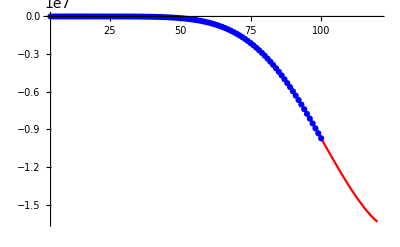

```mathematica
Show[Plot[Im[α[-1,7,2,0][r]],{r,4,120}, PlotStyle->Red],ListPlot[Table[{rs[[i,1]],Im[rs[[i,2]]]},{i,1,Length[rs]}], PlotStyle->Blue], PlotRange->All]
```

```mathematica
R[1,20,0,0]
```

<|In→TeukolskyRadialFunction[…],Up→TeukolskyRadialFunction[…]|>